```mathematica
(*setup information*)
h= 0.01; 
λ=100;
a0= 1; 
c= 0;
```

```mathematica
(*Theoretic Solution*)
Theoα[n_] = (a0 + c / λ) Cos[Sqrt[λ]n h] - c / λ
```

Cos[0.1 n]

```mathematica
(*Implicit Euler*)
M = {{1, -h},{λ h, 1}};
w = {0, -h c};
A = Inverse[M];
 w= A.w;
sol = RSolve[{a[n+1]==A[[1,1]] a[n] + A[[1,2]] b[n] + w[[1]], b[n+1]==A[[2,1]] a[n] + A[[2,2]] b[n] + w[[2]], a[0] == a0, b[0]==0}, {a[n], b[n]}, n]// FullSimplify ;
IEα[n_] = Re[(a[n]/.sol)[[1]]] // FullSimplify
IEβ[n_] = Re[(b[n]/.sol)[[1]]] // FullSimplify
```

Re[0.5 (0.990099-0.0990099 ⅈ)^n+0.5 (0.990099+0.0990099 ⅈ)^n]

-10. Re[ⅇ^(-0.00497517 n) Sin[0.0996687 n]]

```mathematica
(*Newmark-β*)
M = {{1 + h^2 λ β, 0},{λ h / 2, 1}};
w = {-h^2c / 2, - h c};
M1 ={{1 - h ^2 λ(1/2 - β), h}, {-λ h / 2, 1}}
A = Inverse[M].M1;
w = Inverse[M].w;
sol = RSolve[{a[n+1]==A[[1,1]] a[n] + A[[1,2]] b[n] + w[[1]], b[n+1]==A[[2,1]] a[n] + A[[2,2]] b[n] + w[[2]], a[0] == a0, b[0]==0}, {a[n], b[n]}, n]// FullSimplify ;
NMα[n_] = Re[(a[n]/.sol)[[1]]] // FullSimplify
NMβ[n_] = Re[(b[n]/.sol)[[1]]] // FullSimplify
```

{{1-0.01 (1/2-β),0.01},{-0.5,1}}

Re[ⅇ^(-0.693147 n) (0.5 ((199.-1. √(-399.-4. β)+2. β)/(100.+β))^n+0.5 ((199.+√(-399.-4. β)+2. β)/(100.+β))^n)]

-0.25 Re[ⅇ^(-0.693147 n) √(-399.-4. β) (1. ((199.-1. √(-399.-4. β)+2. β)/(100.+β))^n-1. ((199.+√(-399.-4. β)+2. β)/(100.+β))^n)]

```mathematica
error[n] =(NMα[n] /. {β-> 1/4}) - Theoα[n]
```

-Cos[0.1 n]+Re[(0.5 (1.99002-0.199501 ⅈ)^n+0.5 (1.99002+0.199501 ⅈ)^n) ⅇ^(-0.693147 n)]

```mathematica
error[10]
```

error[10]

```mathematica
(*BDF2*)
(*
M = {{1, -2h/3}, {2hλ/3, 1}};
M1 = {{4/3, 0}, {0, 4/3}};
M2 = {{-1/3, 0}, {0, -1/3}};
w = {0, -2h c/3};
A1 = Inverse[M].M1
A2 = Inverse[M].M2;
w = Inverse[M].w;
sol = RSolve[{a[n+2]==A1[[1,1]] a[n+1] + A1[[1,2]] b[n + 1] +  A2[[1,1]] a[n] + A2[[1,2]] b[n] + w[[1]], b[n+2]==A1[[2,1]] a[n + 1] + A1[[2,2]] b[n + 1] +A2[[2,1]] a[n] + A2[[2,2]] b[n]+ w[[2]], a[0] == a0, b[0]==0, a[1] == IEα[1], b[1] == IEβ[1]}, {a[n], b[n]}, n]// FullSimplify ;
BDF2α[n_] = Re[(a[n]/.sol)[[1]]] // FullSimplify
BDF2β[n_] = Re[(b[n]/.sol)[[1]]] // FullSimplify
*)
```

```mathematica
(NMα[10]/.{β-> 1/ 4}) - Theoα[10]
```

0.000699989

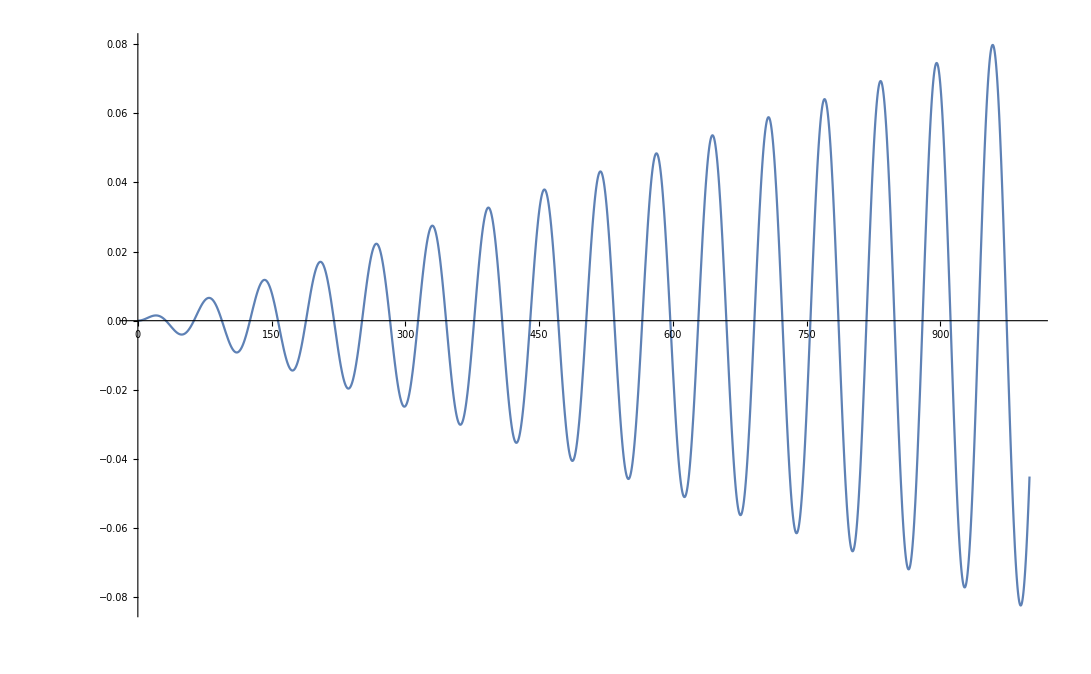

```mathematica
Plot[{(NMα[n]/.{β-> 1/ 4})-Theoα[n]}, {n, 0, 1000}]
```

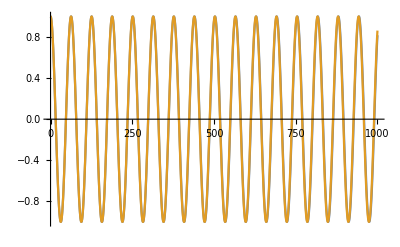

```mathematica
Plot[{(NMα[n]/.{β-> 1/ 4}),Theoα[n]}, {n, 0, 1000}]
```